Practice Problems for Numerical Analysis Final

http://reference.wolfram.com/mathematica/tutorial/KeyboardShortcutListing.html
Solving equations:
	Analytic solutions:
		Quadratic
		Cubic [Closed form]
			Galois theorem for finding all roots (*needs writeup*)

```mathematica
(* Solve the following cubic using the closed form*)
coeff = RandomInteger[{0, 20}, 4];
terms = {x^3, x^2, x,1};
cubic = coeff . terms == 0
NSolve[cubic, x]

(* Solve the following cubic using the closed form*)
cubic = x^3 + 6x^2 + 21x + 52 == 0;
NSolve[cubic, x];

cubic = x^3 + -30x -36 == 0;
NSolve[cubic, x];
```

3+11 x+16 x^2+7 x^3==0

{{x→-1.36399},{x→-0.460863-0.319076 ⅈ},{x→-0.460863+0.319076 ⅈ}}

Quartic [Closed form]

```mathematica
(* Solve the following quartic using the closed form*)
coeff = RandomInteger[{0, 20}, 4];
terms = {x^3, x^2, x,1};
cubic = coeff . terms
NSolve[cubic, x]
```

Quintic [Impossible]
		
	Numerical Methods
		Fixed point iteration

```mathematica
(* Find pi using fixed point iteration*)
N[π]
(* Find the √2 using FP iteration *)
N[√2];
```

3.14159

Error bound
			Convergence rate

```mathematica
(* Prove that the ratio of errors converges to g'(R)*)
```

Mean Value && Intermediate Value Theorem
			(* Need to understand by copying notes into summary sheet *)
		Newtons method

```mathematica
(* Prove that Newton's method converges quadratically to f''(R)/2f'(R)
```

Error bound
			Convergence rate
				Differing under double, triple, roots.

```mathematica
(* show that Newton's method converges only linearly when the underlying function has double roots*)
```

Synthetic Division
			Polynomial Remainder Theorem

```mathematica
(* state the polynomial remainder theorem*)

(* prove polynomial remainder theorem*)

(* show that the polynomial remainder theorem allows us to evaluate higher derivatives*)
```

Evaluating polynomials
				Evaluating derivatives of polynomials

Solving System of Equations:

Linear equations:
	Numerical Methods:
		Gaussian Elimination
			Determining if an equation is solvable
			Running time
		L-U Decomposition

```mathematica
(* Show all details of a *HAND* computation that solves *)
n = 4
A = UpperTriangularize[RandomInteger[{1, 3}, {n, n}]];
B = LowerTriangularize[RandomInteger[{-1, 2}, {n, n}]];
c = RandomInteger[{-5, 5}, {n, 1}];
MatrixForm[A]MatrixForm[B] == MatrixForm[c]

LinearSolve[A * B, c]
```

4

(1 | 0 | 0 | 0
1 | -1 | 0 | 0
1 | 1 | -1 | 0
2 | -1 | 0 | 0) (1 | 2 | 3 | 3
0 | 3 | 3 | 3
0 | 0 | 2 | 3
0 | 0 | 0 | 3)==(1
0
5
0)

{{1},{0},{-5/2},{0}}

Running time
		Gauss-Seidel elimination

```mathematica
(* Solve the following system using Gauss-Seidel elimination *)
```

Convergence

Error bound
		Find the inverse by attaching identity matrix
			Running time
		Error bounds
			Norms
			Condition number of a matrix

```mathematica
(* Given the matrices below, which system is more susceptible to roundoff erros*)
n = 4
Clear[x]
X = Table[x, {n}];
A = RandomInteger[{-1, 3}, {n, n}];
b = RandomInteger[{-1, 2}, {n, 1}];
G = RandomInteger[{-5, 1}, {n, n}];
h = RandomInteger[{-1, 2}, {n, 1}];
MatrixForm[A] MatrixForm[X] == MatrixForm[b]
MatrixForm[G] MatrixForm[X] == MatrixForm[h]
LinearAlgebra`MatrixConditionNumber[A, Norm->∞]
LinearAlgebra`MatrixConditionNumber[G, Norm->∞]
```

4

(x
x
x
x) (0 | 0 | -1 | -1
3 | 2 | 2 | 1
0 | 2 | -1 | 0
0 | 2 | 3 | 3)==(-1
-1
2
2)

(x
x
x
x) (-2 | -4 | -1 | 0
0 | 1 | -3 | -2
-2 | 0 | -2 | -5
-2 | -5 | -4 | -4)==(2
0
-1
1)

48

845/32

Rounding error
				Conversion between decimals and binary fractions

```mathematica
(* Convert the following fraction to decimal *)
r = RandomReal[1, WorkingPrecision->3]

BaseForm[r, 2]

(* Convert the following binary fraction to decimal*)
r = RandomReal[1, WorkingPrecision->3];
BaseForm[r, 2]

r
```

0.0762

0.0001001110000_2

0.1111010011_2

0.956

IEEE 564 representation

```mathematica
(*Convert the following decimal number to its IEEE 754 double precision encoding*)
r = RandomReal[{-5, 5}, WorkingPrecision->5]
binary = RealDigits[r, 2];
binary⟦1⟧ = Drop[binary⟦1⟧, 1];
exp = (binary⟦2⟧-1) + 1023;
exp = IntegerDigits[exp, 2];
signbit = If[r < 0, 1, 0];
ToString[signbit] <> " | " <> StringJoin[ToString /@ PadLeft[exp, 11] ] <> " | " <> StringJoin[ToString /@ PadRight[binary⟦1⟧, 52]]

(*Conver the following IEEE 754 double precision to a decimal number*)
r = RandomReal[{-5, 5}, WorkingPrecision->5];
binary = RealDigits[r, 2];
binary⟦1⟧ = Drop[binary⟦1⟧, 1];
exp = (binary⟦2⟧-1) + 1023;
exp = IntegerDigits[exp, 2];
signbit = If[r < 0, 1, 0];
ToString[signbit] <> " | " <> StringJoin[ToString /@ PadLeft[exp, 11] ] <> " | " <> StringJoin[ToString /@ PadRight[binary⟦1⟧, 52]]
r
```

3.312

0 | 10000000000 | 1010011111110000000000000000000000000000000000000000

1 | 01111111110 | 0000101011000010000000000000000000000000000000000000

-0.52101

Non-linear equations
	Methods:
		Fixed point iteration
		Newtons method
		Fixed point iteration
			Error bound (can compute number of steps from recurrence relation)
Multivariable non-linear systems of equations:
	Methods:

```mathematica
(* Compute one step of Netwons method for the following system of non-linear equations with initial guess)*)
f[x_, y_]:=x^2- 5x y;
g[x_, y_]:=x^3 y- 4 x^2 y^2;
Clear[x];
Clear[y];
Subscript[x, i]=RandomReal[5];
Subscript[y, i]= RandomReal[5];
init = {x->Subscript[x, i], y->Subscript[y, i]}
jac = D[{f[x,y], g[x,y]}, {{x,y}}]/. init;

b = {-f[Subscript[x, i], Subscript[y, i]], -g[Subscript[x, i], Subscript[y, i]]};
LinearSolve[jac, b]//MatrixForm
```

{x→2.04428,y→4.50485}

(14.6631
-30.5429)

Newton's method

Integration:
	Review of the fundamental theorem of calculus

```mathematica
(* State the fundamental theorem of calculus *)

(* Evaluate *)
Clear[h]
Gfunc[h_] :=Integrate[Sin[t^2], {t, 3+5h, h^2+1}];
Gfunc'[h]
```

√(π/2) (-5 √(2/π) Sin[(3+5 h)^2]+2 h √(2/π) Sin[(1+h^2)^2])

Strange limit definition

```mathematica
(*Using Jeff's strange definition of limit sums, find the antiderivative*)
f[x_] := x^2+ 1;
```

Methods:
		Right endpoint

```mathematica
(* Approximate the integral of the following function using the right endpoint rule*)
h = RandomInteger[{1, 5}]
a = RandomInteger[{0, 10}]
b = RandomInteger[{3, 5}] *h
Subscript[ep, i_]:= a + (i + 1)*h;
Sum[N[Sin[Subscript[ep, i]^2]*h], {i, 0, Floor[b/h]}]
```

1

9

3

-0.600572

Left endpoint

```mathematica
(* Approximate the integral of the follwing function using the left endpoint rule *)
h = RandomInteger[{1, 5}]
a = RandomInteger[{0, 10}]
b = RandomInteger[{3, 5}] *h
Subscript[ep, i_]:= a + i*h;
Sum[N[Sin[Subscript[ep, i]^2]*h], {i, 0, Floor[b/h]}]
```

4

9

12

-1.33976

Trapezoid rule

```mathematica
(* prove that the trapezoid rule is really 1/2(f(a) + f(b)) *)

(* evaluate the following function's integral over the interval using the trapezoid rule*)
h = RandomInteger[{1, 5}]
a = RandomInteger[{0, 10}]
b = RandomInteger[{3, 5}] *h
Subscript[ep, i_]:= a + i*h;
Sum[N[Sin[Subscript[ep, i]^2]*h], {i, 0, Floor[b/h]}]
```

Error analysis (*needs a clean rewrite*)
			local vs global error
		Simpsons rule
			⅜ rule
				error analysis (*needs a clean rewrite*)
				local vs global error
			⅓ rule
				error analysis (*needs a clean rewrite*)

```mathematica
(* Prove the error bound of M4 h^5/90 for local error and m4 (b - a) h^4/180 for global error*)
```

local vs global error
		Gaussian integration
			Error analysis

```mathematica
(*Prove the error bound for quadrature integration*)
```

Fitting data:
	Linear regression
		Least squares

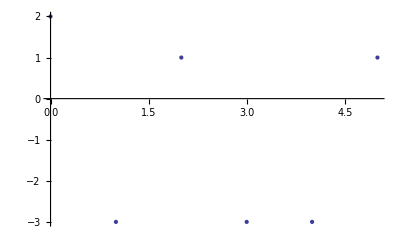

-0.190476-0.257143 x

```mathematica
(* Fit the following data points with a line using least squared regression *)
points = Table[{i, RandomInteger[{-3,3}]}, {i, 0, 5}];
ListPlot[points]
Clear[x];
Normal[LinearModelFit[points, x,x]]

(* Derive the least squares estimator for alpha + beta*x *)
```

Interpolating polynomials

```mathematica
(* Find an interpolating polynomial between these three points for the *)
```

Newton interpolating polynomials
		Cubic Splines (better than interpolating polynomials)

```mathematica
(* Find two cubic splines between these three points*)
```

Blending polynomials

```mathematica
(* Find the blending polynomial between these three points *)
```

Differentiation:
	Discrete difference approximation

```mathematica
(* Explian why the discrete difference method is bad *)
```

Taylor polynomials

```mathematica
(* Derive a taylor chain for ln[u]*)

(* Derive a taylor chain for e^u*)
```